We are interested in deriving formulas for the sequence of jump amplitudes of a 1D chain given by the cut and project method.
We call α the (irrational) slope of the quasicrystal line.

A point of the lattice writes x = n e_x + m e_y where e_x and e_y are the generating vectors of the superlattice (here a square), and n, m integers.
x is in the selected band iff n(1+α) ≤ l < (n+1)(1+α), with l = n+m.
This is equivalent to n = IntegerPart[l/(1+α)].

Note that l can serve as a labelling of the sites on the quasicrystal. It is the standard (real space) labelling.
If l → l+1, then either n or m has increased by 1. If n has increased by 1, we have a coupling t_w btw sites l and l+1.
If n has not increased (ie m has increased by 1), we have a coupling t_s btw sites l and l+1.

This translates into the following function taking value 1 (n has increased) or 0 (m has increased).

```mathematica
α=1/GoldenRatio//N;
```

```mathematica
α=1/√2//N;
```

```mathematica
fib[n_]:=IntegerPart[(1+α)^-1( n+1)]-IntegerPart[(1+α)^-1 (n)];
```

This translates into a condition on mods:

```mathematica
fib2[n_]:=(1-Mod[n+1,1+α]+Mod[n,1+α])/(1+α)
```

```mathematica
Fibonacci[2]
```

1

```mathematica
fib/@Range[Fibonacci[4]]
```

{1,0,1}

```mathematica
n=20;
fib2/@Range[Fibonacci[n]]==fib/@Range[Fibonacci[n]]
```

True

A more elegant condition on mods

```mathematica
fib5[n_]:=If[Mod[n,1+α]≥α,1,0];
```

```mathematica
n=20;
fib5/@Range[Fibonacci[n]]==fib/@Range[Fibonacci[n]]
```

True

Now, if α=p/q is a rational, we easily get:

```mathematica
n=6;
p=Fibonacci[n-2];
q=Fibonacci[n-1];
α=p/q;
```

```mathematica
fib6[n_]:=If[Mod[q n,p+q]≥p,1,0];
```

By the way, this proves that the chain is p+q periodic.

```mathematica
fib6/@Range[p+q]
```

{1,0,1,1,0,1,1,0}

```mathematica
fib6/@Range[p+q]==fib/@Range[q+p]
```

True

Another condition mentionned in a talk by Eric Akkermans, involving a Cos function. It looks like a sharpened version of the Harper potential!

```mathematica
eric[n_]:=(Sign[Cos[2Pi n/(1+α)+Pi/(1+α)]-Cos[Pi/(1+α)]]+1)/2
```

```mathematica
α=1/GoldenRatio//N
```

0.618034

```mathematica
n=10;
fib/@Range[Fibonacci[n]]==eric/@Range[Fibonacci[n]]
```

True

```mathematica
eric/@Range[Fibonacci[n]]
```

{1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,0,1}

```mathematica
fib/@Range[Fibonacci[n]]
```

{1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,0,1}

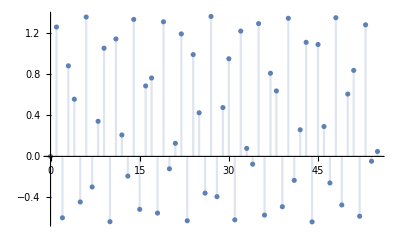

```mathematica
DiscretePlot[Cos[2Pi n/(1+α)+Pi/(1+α)]-Cos[Pi/(1+α)],{n,0,Fibonacci[10]}]
```

```mathematica
(* positive part between angles θ1 and θ2 *)
Manipulate[PolarPlot[(Sign[Cos[x-ϕ]-Cos[Pi/(1+α)]]+1)/2,{x,0,2 Pi},PlotRange->{{-1,1},{-1,1}},Epilog->{Point[{Cos[π/(1+α)+ϕ],Sin[π/(1+α)+ϕ]}],Point[{Cos[-π/(1+α)+ϕ],Sin[-π/(1+α)+ϕ]}]}],{ϕ,0,2Pi},{α,0,1}]
```

```mathematica
test[n_]:=If[Mod[n+1,α+1]-Mod[n,α+1]<0,1,0];
```

```mathematica
n=10;
test/@Range[Fibonacci[n]]
```

{1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,0,1}

```mathematica
fib/@Range[Fibonacci[n]]
```

{1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,0,1}

Going from standard to co-numerotation.

```mathematica
conum[n_]:=Mod[q n,p+q];
```

```mathematica
conum/@Range[0,p+q-1]
```

{0,5,2,7,4,1,6,3}

Let’s build the Hamiltonian in the direct basis, and then go to the co-numbered basis!

```mathematica
(* Mathematica starts at n=1 rather than 0 *)
jump[n_]:=If[conum[n-1]≥p,Subscript[t, w],Subscript[t, s]];
```

```mathematica
h[n_]:=Block[{L=n,tbl,ar},
tbl=Table[{i,i+1}->jump[i],{i,1,L-1}];
(* periodic boundary conditions *)
AppendTo[tbl,{1,L}->jump[L]];
ar=SparseArray[tbl,{L,L}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
n=6;
p=Fibonacci[n-2];
q=Fibonacci[n-1];
α=p/q;
htest=h[Fibonacci[n]];
jump/@Range[p+q]
```

{t_s,t_w,t_s,t_w,t_w,t_s,t_w,t_w}

```mathematica
(* Mathematica starts at index 1 rather than 0 *)
co=conum/@Range[0,p+q-1]+1;
perm=Table[DiscreteDelta[i-co[[j]]],{i,p+q},{j,p+q}];
perm.htest.Transpose[perm]//MatrixForm
```

(0 | 0 | 0 | t_w | 0 | t_s | 0 | 0
0 | 0 | 0 | 0 | t_w | 0 | t_s | 0
0 | 0 | 0 | 0 | 0 | t_w | 0 | t_s
t_w | 0 | 0 | 0 | 0 | 0 | t_w | 0
0 | t_w | 0 | 0 | 0 | 0 | 0 | t_w
t_s | 0 | t_w | 0 | 0 | 0 | 0 | 0
0 | t_s | 0 | t_w | 0 | 0 | 0 | 0
0 | 0 | t_s | 0 | t_w | 0 | 0 | 0)

```mathematica
htest//MatrixForm
```

(0 | t_s | 0 | 0 | 0 | 0 | 0 | t_w
t_s | 0 | t_w | 0 | 0 | 0 | 0 | 0
0 | t_w | 0 | t_s | 0 | 0 | 0 | 0
0 | 0 | t_s | 0 | t_w | 0 | 0 | 0
0 | 0 | 0 | t_w | 0 | t_w | 0 | 0
0 | 0 | 0 | 0 | t_w | 0 | t_s | 0
0 | 0 | 0 | 0 | 0 | t_s | 0 | t_w
t_w | 0 | 0 | 0 | 0 | 0 | t_w | 0)

Test with silver ratio instead of golden ratio

```mathematica
(* silver numbers *)
Ag[n_]:=Ag[n]=2 Ag[n-1]+Ag[n-2];
Ag[0]=0;
Ag[1]=1;
```

```mathematica
n=4;
p=Ag[n-2];
q=Ag[n-1];
α=p/q;
htest=h[Ag[n-2]+Ag[n-1]];
jump/@Range[p+q]
```

{t_s,t_w,t_w,t_s,t_w,t_w,t_w}

```mathematica
(* Mathematica starts at index 1 rather than 0 *)
co=conum/@Range[0,p+q-1]+1;
perm=Table[DiscreteDelta[i-co[[j]]],{i,p+q},{j,p+q}];
perm.htest.Transpose[perm]//MatrixForm;
```